```mathematica
Clear["Global`*"]
F[x1_,x2_]=(a-x1)^2+b(x2-x1^2)^2; (*функція Pозенброка*)
a=1; b=100;
x0 = {-0.5,0.5}; (*початкова точка, яка задана*)
α=1.2; (*коефіціент зменшення кроку*)
ϵ=10^-3; (*параметр закінчення пошуку*)
deltaX={1.,1.};(*вектор  прирощень*)
```

```mathematica
(*знайдемо мінімум за допомогою вбудованої функції*)
min=Minimize[F[x1,x2],{x1,x2}]
```

{0,{x1→1,x2→1}}

```mathematica
(*метод Хука-Дживса*)
method[F_,xk1_,xk2_,deltaX_,ϵ_,α_]:=(
t0=AbsoluteTime[]; (*початок часу роботи методу*)
res1={{"k","x_1","x_2","Δ^(k)","F^(k)"}}; (*масив з ітераційним процесом*)
AppendTo[res1,{0,xk1,xk2,deltaX,F[xk1,xk2]}];
step=2; (*крок методу*)
count=0;(*реальна кількість ітерацій*)
k=1; (*кількість кроків*)
res={{"k","step","x^(k - 1)","x^(k)","x^(k + 1)","Δ^(k)"}}; (*масив з детальним описом ітерацій*)
XkPrevios1=xk1;
XkPrevios2=xk2;
deltaXk=deltaX;
While[step≠0,{
If[k≥1000,Break[]];
Switch[step,
2,{
(*досліджуючий пошук*)
Xk2=XkPrevios2;
Xk1=XkPrevios1;
x1Right = XkPrevios1 +deltaXk[[1]];
x2Right = XkPrevios2 +deltaXk[[2]];
x1Left= XkPrevios1 -deltaXk[[1]];
x2Left = XkPrevios2 -deltaXk[[2]];
(*змінюємо першу змінну, якщо значення функції в новій точці менше минулого*)
If[F[x1Right,Xk2]<F[Xk1,Xk2]&&F[x1Right,Xk2]<F[x1Left,Xk2] ,Xk1=x1Right];
If[F[x1Left,Xk2]<F[Xk1,Xk2]&&F[x1Left,Xk2]<F[x1Right,Xk2] ,Xk1=x1Left];

(*змінюємо другу змінну, якщо значення функції в новій точці менше минулого*)
If[F[Xk1,x2Right]<F[Xk1,Xk2]&&F[Xk1,x2Right]<F[Xk1,x2Left] ,Xk2=x2Right];
If[F[Xk1,x2Left]<F[Xk1,Xk2]&&F[Xk1,x2Left]<F[Xk1,x2Right] ,Xk2=x2Left];

AppendTo[res,{k,step,{XkPrevios1,XkPrevios2},{Xk1,Xk2},{XkNext1,XkNext2},deltaXk}];
step=3;
k++;
Continue[];
},
3,{
(*перевіряємо чи був досліджуючий пошук вдалий*)
(*якщо дві змінні змінені, то пошук вдалий*)
If[XkPrevios1≠Xk1 && XkPrevios2≠Xk2,
{
(*якщо так, то переходимо до пошуку за зразком*)
AppendTo[res,{k,step,{XkPrevios1,XkPrevios2},{Xk1,Xk2},{XkNext1,XkNext2},deltaXk}];
step=5;
k++;
Continue[];
},{
(*якщо ні, то перевіряємо умову закінчення пошуку*)
AppendTo[res,{k,step,{XkPrevios1,XkPrevios2},{Xk1,Xk2},{XkNext1,XkNext2},deltaXk}];
step=4;
k++;
Continue[];
}
];
},
4,{
(*перевірка умови закінчення пошуку*)
If[Norm[deltaXk]<ϵ,
{
(*якщо нерівність виконується, тоді припиняємо пошук*)
AppendTo[res,{k,step,{XkPrevios1,XkPrevios2},{Xk1,Xk2},{XkNext1,XkNext2},deltaXk}];
step=0;
k++;
Continue[];
},{
(*якщо нерівність не виконується, тоді зменщуємо прирощення*)
deltaXk/=α;
AppendTo[res,{k,step,{XkPrevios1,XkPrevios2},{Xk1,Xk2},{XkNext1,XkNext2},deltaXk}];
step=2;
k++;
Continue[];
}];

},
5,{
(*пошук за зразком*)
XTemp1=Xk1+(Xk1-XkPrevios1);
XTemp2=Xk2+(Xk2-XkPrevios2);
AppendTo[res,{k,step,{XkPrevios1,XkPrevios2},{XTemp1,XTemp2},{XkNext1,XkNext2},deltaXk}];
step=6;
k++;
Continue[];
},
6,{
(*досліджуючий пошук*)
XkNext1=XTemp1;
XkNext2=XTemp2;
x1Right = XkNext1 +deltaXk[[1]];
x1Left = XkNext1 -deltaXk[[1]];
x2Right = XkNext2 +deltaXk[[2]];
x2Left= XkNext2 -deltaXk[[2]];

(*змінюємо першу змінну, якщо значення функції в новій точці менше минулого*)
If[F[x1Right,XkNext2]<F[XkNext1,XkNext2]&&F[x1Right,XkNext2]<F[x1Left,XkNext2] ,XkNext1=x1Right];
If[F[x1Left,XkNext2]<F[XkNext1,XkNext2]&&F[x1Left,XkNext2]<F[x1Right,XkNext2] ,XkNext1=x1Left];

(*змінюємо другу змінну, якщо значення функції в новій точці менше минулого*)
If[F[XkNext1,x2Right]<F[XkNext1,XkNext2]&&F[XkNext1,x2Right]<F[XkNext1,x2Left] ,XkNext2=x2Right];
If[F[XkNext1,x2Left]<F[XkNext1,XkNext2]&&F[XkNext1,x2Left]<F[XkNext1,x2Right] ,XkNext2=x2Left];


AppendTo[res,{k,step,{XkPrevios1,XkPrevios2},{Xk1,Xk2},{XkNext1,XkNext2},deltaXk}];
step=7;
k++;
Continue[];
},
7,{
(*перевіряємо чи був досліджуючий пошук вдалий*)
If[F[XkNext1,XkNext2]<F[Xk1,Xk2],{
(*якщо вдалий, то записуємо точку та переходимо до пошуку за зразком*)
XkPrevios1=Xk1;
XkPrevios2=Xk2;
Xk1=XkNext1;
Xk2=XkNext2;
Clear[XkNext1,XkNext2];
AppendTo[res,{k,step,{XkPrevios1,XkPrevios2},{Xk1,Xk2},{XkNext1,XkNext2},deltaXk}];
count++;
AppendTo[res1,{count,Xk1,Xk2,deltaXk,F[Xk1,Xk2]}];
step=5;
k++;
Continue[];
},{ 
(*якщо вдалий, то перевіряємо умову закінчення пошуку*)
AppendTo[res,{k,step,{XkPrevios1,XkPrevios2},{Xk1,Xk2},{XkNext1,XkNext2},deltaXk}];
step=4;
k++;
Continue[];
}];
step=0;
}
]}];
t1=AbsoluteTime[]; (*кінець часу роботи методу*)
Print["Час роботи методу: ",t=t1-t0, "\nНев'язка: ",Norm[min[[2,1;;2,2]]-{Xk1,Xk2} ],"\nФактична похибка: ",Abs[F[min[[2,1,2]],min[[2,2,2]]]-F[Xk1,Xk2] ],"\nЛокальна похибка: ",Norm[deltaXk]];
AppendTo[res,{k,step,{XkPrevios1,XkPrevios2},{Xk1,Xk2},{XkNext1,XkNext2},deltaXk}];
Return[Print["Отримане значення: ",{Xk1,Xk2}]];
)
```

```mathematica
(*виклик методу*)method[F,x0[[1]],x0[[2]],deltaX,ϵ,α]
(*виведення таблиці з детальним описом ітерацій*)
Grid[res];
(*виведення таблиці з результатом ітераційного процесу*)
Grid[res1]
```

Час роботи методу: 0.0092336
Нев'язка: 0.000894352
Фактична похибка: 4.37167×10^-6
Локальна похибка: 0.0009622

Отримане значення: {1.00032,1.00084}

k | x_1 | x_2 | Δ^(k) | F^(k)
0 | -0.5 | 0.5 | {1.,1.} | 8.5
1 | -0.593464 | 0.313072 | {0.0934639,0.0934639} | 2.69222
2 | -0.5 | 0.219608 | {0.0934639,0.0934639} | 2.34237
3 | -0.313072 | 0.126144 | {0.0934639,0.0934639} | 1.80329
4 | -0.0326806 | 0.0326806 | {0.0934639,0.0934639} | 1.16636
5 | 0.154247 | 0.0326806 | {0.0934639,0.0934639} | 0.723198
6 | 0.247711 | 0.0326806 | {0.0934639,0.0934639} | 0.648194
7 | 0.185695 | 0.022198 | {0.0104826,0.0104826} | 0.678184
8 | 0.20666 | 0.0326806 | {0.0104826,0.0104826} | 0.639444
9 | 0.238108 | 0.0536458 | {0.0104826,0.0104826} | 0.58141
10 | 0.280038 | 0.074611 | {0.0104826,0.0104826} | 0.519797
11 | 0.321969 | 0.106059 | {0.0104826,0.0104826} | 0.4603
12 | 0.374382 | 0.137507 | {0.0104826,0.0104826} | 0.392103
13 | 0.416312 | 0.168954 | {0.0104826,0.0104826} | 0.342594
14 | 0.458242 | 0.210885 | {0.0104826,0.0104826} | 0.293582
15 | 0.510655 | 0.263298 | {0.0104826,0.0104826} | 0.240098
16 | 0.563068 | 0.315711 | {0.0104826,0.0104826} | 0.191088
17 | 0.604999 | 0.368124 | {0.0104826,0.0104826} | 0.156467
18 | 0.646929 | 0.420537 | {0.0104826,0.0104826} | 0.125067
19 | 0.68886 | 0.47295 | {0.0104826,0.0104826} | 0.0970573
20 | 0.73079 | 0.535845 | {0.0104826,0.0104826} | 0.0727949
21 | 0.77272 | 0.598741 | {0.0104826,0.0104826} | 0.0519264
22 | 0.814651 | 0.661636 | {0.0104826,0.0104826} | 0.0347622
23 | 0.856581 | 0.735015 | {0.0104826,0.0104826} | 0.0207337
24 | 0.898511 | 0.808393 | {0.0104826,0.0104826} | 0.0104144
25 | 0.940442 | 0.881771 | {0.0104826,0.0104826} | 0.00425473
26 | 0.982372 | 0.965632 | {0.0104826,0.0104826} | 0.000343966
27 | 0.939761 | 0.883132 | {0.000680378,0.000680378} | 0.00362872
28 | 0.940442 | 0.884492 | {0.000680378,0.000680378} | 0.00354755
29 | 0.941122 | 0.885853 | {0.000680378,0.000680378} | 0.00346861
30 | 0.941803 | 0.887214 | {0.000680378,0.000680378} | 0.00339185
31 | 0.942483 | 0.888575 | {0.000680378,0.000680378} | 0.00331724
32 | 0.943844 | 0.890616 | {0.000680378,0.000680378} | 0.0031586
33 | 0.945204 | 0.893337 | {0.000680378,0.000680378} | 0.0030031
34 | 0.946565 | 0.896059 | {0.000680378,0.000680378} | 0.00285581
35 | 0.947926 | 0.89878 | {0.000680378,0.000680378} | 0.00271639
36 | 0.949287 | 0.900821 | {0.000680378,0.000680378} | 0.00258232
37 | 0.950648 | 0.903543 | {0.000680378,0.000680378} | 0.00243919
38 | 0.952008 | 0.906264 | {0.000680378,0.000680378} | 0.00230351
39 | 0.953369 | 0.908986 | {0.000680378,0.000680378} | 0.00217499
40 | 0.95473 | 0.911708 | {0.000680378,0.000680378} | 0.00205333
41 | 0.956091 | 0.914429 | {0.000680378,0.000680378} | 0.00193827
42 | 0.958132 | 0.917831 | {0.000680378,0.000680378} | 0.00175639
43 | 0.960173 | 0.921913 | {0.000680378,0.000680378} | 0.00158624
44 | 0.962214 | 0.925995 | {0.000680378,0.000680378} | 0.00142974
45 | 0.964255 | 0.930078 | {0.000680378,0.000680378} | 0.0012861
46 | 0.966296 | 0.93348 | {0.000680378,0.000680378} | 0.00114213
47 | 0.968337 | 0.937562 | {0.000680378,0.000680378} | 0.00100385
48 | 0.970378 | 0.941644 | {0.000680378,0.000680378} | 0.000877444
49 | 0.97242 | 0.945726 | {0.000680378,0.000680378} | 0.000762278
50 | 0.974461 | 0.949809 | {0.000680378,0.000680378} | 0.000657772
51 | 0.976502 | 0.953891 | {0.000680378,0.000680378} | 0.000563385
52 | 0.978543 | 0.957293 | {0.000680378,0.000680378} | 0.000466834
53 | 0.979904 | 0.960014 | {0.000680378,0.000680378} | 0.000407742
54 | 0.981265 | 0.962736 | {0.000680378,0.000680378} | 0.000353098
55 | 0.982625 | 0.965457 | {0.000680378,0.000680378} | 0.000302785
56 | 0.983986 | 0.968179 | {0.000680378,0.000680378} | 0.000256694
57 | 0.985347 | 0.9709 | {0.000680378,0.000680378} | 0.000214723
58 | 0.986708 | 0.973622 | {0.000680378,0.000680378} | 0.00017678
59 | 0.988068 | 0.976343 | {0.000680378,0.000680378} | 0.000142781
60 | 0.989429 | 0.979065 | {0.000680378,0.000680378} | 0.000112648
61 | 0.99079 | 0.981786 | {0.000680378,0.000680378} | 0.0000863152
62 | 0.992151 | 0.984508 | {0.000680378,0.000680378} | 0.0000637214
63 | 0.993511 | 0.987229 | {0.000680378,0.000680378} | 0.0000448153
64 | 0.994872 | 0.989951 | {0.000680378,0.000680378} | 0.0000295536
65 | 0.996233 | 0.992672 | {0.000680378,0.000680378} | 0.0000179012
66 | 0.997594 | 0.995394 | {0.000680378,0.000680378} | 9.83114×10^-6
67 | 0.998954 | 0.998115 | {0.000680378,0.000680378} | 5.32477×10^-6
68 | 1.00032 | 1.00084 | {0.000680378,0.000680378} | 4.37167×10^-6

Траєкторія пошука мінімума

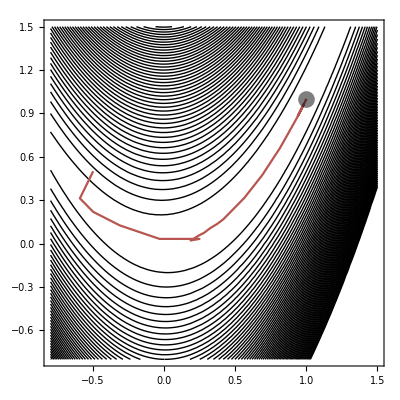

```mathematica
CP=ContourPlot[F[x1,x2],{x1,-0.8,1.5},{x2,-0.8,1.5},ContourShading->None,Contours->{Automatic,100}];
Print["Траєкторія пошука мінімума"];
Show[CP,ListLinePlot[res1[[1;;-1,{2,3}]],ColorFunction->"Rainbow",PlotRange->All],Graphics[{Opacity[0.5],Black,PointSize[0.03],Point[{1,1}]}]]
```